```mathematica
res={{0.0017208526392639418,0.0022570683082295305,0.0024384452350511695,0.002031280653647367,0.001302893360279656,0.002027057040596857,0.0016306675402180271,0.0013433708177637638,0.0020063069499711133,0.0019122537324666308,0.0016098976555113838,0.0019539015615843446,0.001544063057262815,0.0017151175928020292,0.0011484299038048184,0.001034632543292689,0.0013108815057241154,0.0017267504232501658,0.001029860305779289,0.001161005127781706,0.001486636931322796,0.0012641584387586566,0.00142518502662603,0.00128990783962317,0.0013802270058430343,0.0017725624831756903,0.0014537056520741093,0.0015691478563276515,0.0010690941269016541,0.0014130853399092847,0.0010692480059090424,0.00091959726273635,0.0012514901027151156,0.0014901657810099979,0.0012957077538623088,0.0015246920016131833,0.0014386004250125472,0.0012397096244007525,0.0011825433601254948,0.0012438090761940318,0.0017569453083966541,0.0016701581518159198,0.0011641731571152888,0.0014342128317600016,0.0010650211441439097,0.0017334354613274888,0.0015653762051655935,0.0013442778127299014,0.0015429873244142101,0.0013843011602683477,0.0021189906937165754,0.0018372725468461535,0.0020238854074978727,0.0013992374186644365,0.002218216805785421,0.002195664761448792,0.0022543513886625313,0.0017601963486022429,0.0020541595044730374,0.0014607612388963813,0.00241460087689107,0.0024563853473008775,0.0022525906208419487,0.002351220300860583,0.0030926162109379198,0.002572720166964029,0.002734396408993306,0.0024426463733874023,0.002231075928364772,0.0029022374686992927,0.0033862729402343566,0.0026399088933766,0.0028109865072164144,0.003629941040782906,0.003977512834376162,0.0038882190725570537,0.004473119126740902,0.004313268697834824,0.005132288329961547,0.005724791352752833,0.005621931153946048,0.007034890965652604,0.005055067448525411,0.005999366002228234,0.006998523948783369,0.008576689864101124,0.0056775348574978025,0.008576746104144432,0.00863888052295265,0.00888505758982725,0.009086528721971568,0.009158985461052052,0.007484755356125646,0.0076136764773499736,0.010525522756277125,0.010788500328917781,0.013664952217078235,0.013538840044582685,0.011240126268323119,0.015324361792409794,0.01486051727753454,0.014203865189055313,0.015619504391461585,0.013775278867468136,0.016357364084548066,0.016017256736501027,0.013633406843038223,0.014473942339309692,0.016862766068117912,0.016565684767547908,0.0162939689691882,0.0177890900163879,0.017067790033629515,0.01802688847072442,0.015575715694912397,0.016008672016986046,0.020193866496218425,0.019610511463249623,0.01968472435449057,0.017948702046448776,0.013785334828646398,0.017028013109083865,0.013276893006826536,0.01479368044194851,0.013158740859753791,0.011667591304046812,0.008504750664787872,0.011115445145742727,0.009737988902917246,0.010115987518578024,0.009174401109009231,0.007951205606416621,0.0076152678859492265,0.008503866304308863,0.006719732148181627,0.00687434903985038,0.006187838707620268,0.007126700315494781,0.005601429048536525,0.0073245343429695405,0.0058207487785924,0.006191640342820567,0.0045066463942263265,0.005401024187137567,0.004649527401958492,0.005381257249869943,0.004717132176873274,0.0049302224167531395,0.004854336881294824,0.004990774391994259,0.0037277112848871793,0.0038962148870983282,0.0037931580434178874,0.00361737783527487,0.0026448971082785426,0.0028490605194658332,0.0031949771018349444,0.0030600957076873827,0.002962266471896267,0.0028684211011175,0.002804653306708015,0.0026975802528893074,0.0020763875294692357,0.002793465443647995,0.002410570890782598,0.0027715645801916168,0.0027964718538672187,0.0033778099853838508,0.0030854543041600353,0.0022820882927747574,0.002795122021817636,0.00199255096912535,0.0026749149296018083,0.0030594641078575645,0.002381355200178049,0.00293629880356569,0.002184671288689983,0.0021644881431472987,0.0014112629707786375,0.0018276973244219384}};
```

```mathematica
res=Import/@FileNames["*.csv",{"/Users/scherf/Desktop"}];
```

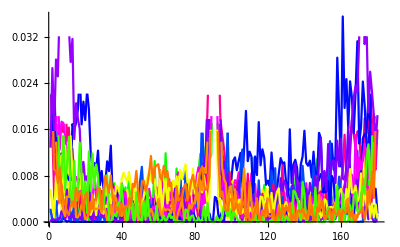

```mathematica
Show[ListLinePlot[#,PlotStyle->Hue[RandomReal[]]]&/@res,PlotRange->All]
```